```mathematica
SetDirectory[NotebookDirectory[]];
<<CIP`CurveFit`
```

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

## Datenimport

Die importierten Daten haben einen Header: “Zeit”,”Temperatur T1”,”Temperatur T2”,”Temperatur T3”,”Temperatur T4”, worauf die Messdaten ab der 4. Zeile folgen.

```mathematica
rawDataMeasurement1=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\data\\Gruppe_3_Messung_1.tsv"];
rawDataMeasurement2=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\data\\Gruppe_3_Messung_2.tsv"];
```

```mathematica
rawDataMeasurement1T=Transpose[Drop[rawDataMeasurement1,{1,3}]];
rawDataMeasurement2T=Transpose[Drop[rawDataMeasurement2,{1,3}]];
```

## Bestimmung der Gefrierpunkterniedrigung

Die Gefrierpunkterniedrigung wird im folgenden Code mit fpd abgekürzt.

```mathematica
convertCelsiusToKelvin[aTemperatureInCelsius_]:=Module[
{},
tmpTemperatureInKelvin=aTemperatureInCelsius+273.15;
tmpTemperatureInKelvin
]
freezingPointDepression[aListOfTemperatures_,theBeginOfConstantRegion_,theEndOfConstantRegion_]:=Module[
{},
tmpListOfConstantTemperatureRegion=Take[aListOfTemperatures,{theBeginOfConstantRegion,theEndOfConstantRegion}];
tmpMeanOfConstantTemperatureRegion=Mean[tmpListOfConstantTemperatureRegion];
tmpSdOfConstantTemperatureRegion=StandardDeviation[tmpListOfConstantTemperatureRegion];
tmpAroundObject=Around[tmpMeanOfConstantTemperatureRegion,tmpSdOfConstantTemperatureRegion];
{tmpAroundObject,tmpMeanOfConstantTemperatureRegion,tmpSdOfConstantTemperatureRegion}
]
```

```mathematica
(*Diese beiden Zeilen dienen des Belegs für den gewählten konstanten Bereich.*)
Take[rawDataMeasurement1T[[3]],{625,Length[rawDataMeasurement1T[[3]]]}];
Take[rawDataMeasurement1T[[5]],{495,Length[rawDataMeasurement1T[[5]]]}];
```

```mathematica
fpdWaterMeasurementG2=freezingPointDepression[rawDataMeasurement1T[[5]],495,Length[rawDataMeasurement1T[[5]]]]
fpdSugarMeasurementG1=freezingPointDepression[rawDataMeasurement1T[[3]],625,Length[rawDataMeasurement1T[[3]]]]
Length[rawDataMeasurement1T[[5]]]-495
```

{0.1120.021,0.111672,0.0214604}

{-0.5370.021,-0.536748,0.0212824}

292

```mathematica
deltaT[temperatureWater_,temperatureSugar_]:=temperatureSugar-temperatureWater
sdDeltaT[sTempWater_,sTempSugar_]:=Sqrt[
(D[deltaT[temperatureWater,temperatureSugar],temperatureWater]*sTempWater)^2+
(D[deltaT[temperatureWater,temperatureSugar],temperatureSugar]*sTempSugar)^2
]
D[deltaT[temperatureWater,temperatureSugar],temperatureWater]
D[deltaT[temperatureWater,temperatureSugar],temperatureSugar]
```

-1

1

```mathematica
(*Diese beiden Zeilen dienen des Belegs für den gewählten konstanten Bereich.*)
Take[rawDataMeasurement2T[[3]],{645,Length[rawDataMeasurement2T[[3]]]}];
Take[rawDataMeasurement2T[[5]],{500,690}];
Length[rawDataMeasurement2T[[3]]]-645
```

127

```mathematica
fpdWaterMeasurementG1=freezingPointDepression[rawDataMeasurement2T[[3]],645,Length[rawDataMeasurement2T[[3]]]]
fpdSugarMeasurementG2=freezingPointDepression[rawDataMeasurement2T[[5]],500,690]
```

{-0.380.20,-0.384766,0.197376}

{-0.6890.022,-0.689267,0.0219206}

Die Gefriererniedrigung von Wasser aus der ersten Messung beträgt: 0.112 +- 0.021 °C und von Zucker Saccharose -0.537 +- 0.021 °C

```mathematica
deltaT[fpdWaterMeasurementG1,fpdSugarMeasurementG1]
deltaT[fpdWaterMeasurementG2,fpdSugarMeasurementG2]
```

{-0.150.20,-0.151983,-0.176094}

{-0.8010.031,-0.800939,0.000460172}

## Bestimmung der kryoskopischen Konstanten für Saccharose

```mathematica
kryoscopicConstant[m1_,m2_,M1_,deltaTemperature_]:=m2/m1*M1*deltaTemperature/1000
sdCryoscopicConstant[sdm1_,sdm2_,sddeltaT_]:=Sqrt[
(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m1]*sdm1)^2+(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m2]*sdm2)^2+(D[kryoscopicConstant[m1,m2,M1,deltaTemperature],deltaTemperature]*sddeltaT)^2
]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m1]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],m2]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],M1]
D[kryoscopicConstant[m1,m2,M1,deltaTemperature],deltaTemperature]
```

-(deltaTemperature M1 m2)/(1000 m1^2)

(deltaTemperature M1)/(1000 m1)

(deltaTemperature m2)/(1000 m1)

(M1 m2)/(1000 m1)

```mathematica
massSugarG1={Around[7.99,0.01],7.99,0.01}
massSugarG2={Around[8.01,0.01],8.01,0.01}
massWaterG1={Around[100.38,0.01],100.38,0.01}
massWaterG2={Around[100,0.01],100,0.01}
molarMassSaccharose=342.30;
```

{7.9900.010,7.99,0.01}

{8.0100.010,8.01,0.01}

{100.3800.010,100.38,0.01}

{100.0000.010,100,0.01}

```mathematica
cryoscopicConstantSaccharose=kryoscopicConstant[massSugarG1[[2]],massWaterG1[[2]],molarMassSaccharose,deltaT[fpdWaterMeasurementG1[[2]],fpdSugarMeasurementG1[[2]]]]

dTemp=deltaT[fpdWaterMeasurementG1[[2]],fpdSugarMeasurementG1[[2]]]
pt1=((molarMassSaccharose/massWaterG1[[2]])*dTemp*massWaterG1[[3]])^2;
pt2=(((massWaterG1[[2]]*molarMassSaccharose*dTemp)/massSugarG1[[2]]^2)*massSugarG1[[3]])^2;
pt3=((molarMassSaccharose*massWaterG1[[2]]/massSugarG1[[2]])*sdDeltaT[fpdWaterMeasurementG1[[3]],fpdSugarMeasurementG1[[3]]])^2;

standardDeviationOfCryoscopicConstant=Sqrt[pt1+pt2+pt3]
Around[cryoscopicConstantSaccharose,standardDeviationOfCryoscopicConstant]
```

-0.653585

-0.151983

853.715

0.854.

```mathematica
100.34/7.99*342.30*0.151983
```

653.325

```mathematica
sdDeltaT[fpdWaterMeasurementG1[[3]],fpdSugarMeasurementG1[[3]]]
```

0.19852

## Bestimmung des Molekulargewichtes

```mathematica
molarMass[m1_,m2_,kryoscopicConstant_,deltaTemperature_]:=m1/m2*kryoscopicConstant/deltaTemperature
sdMolarMass[sdm1_,sdm2_,sddeltaT_,aSdCryoscopicConstant_]:=Sqrt[
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m1]*sdm1)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m2]*sdm2)^2+(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],cryoscopicConstant]*aSdCryoscopicConstant)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],deltaTemperature]*sddeltaT)^2
]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m1]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m2]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],cryoscopicConstant]
D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],deltaTemperature]
```

cryoscopicConstant/(deltaTemperature m2)

-(cryoscopicConstant m1)/(deltaTemperature m2^2)

m1/(deltaTemperature m2)

-(cryoscopicConstant m1)/(deltaTemperature^2 m2)

```mathematica
Sqrt[
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m1]*sdm1)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],m2]*sdm2)^2+(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],cryoscopicConstant]*aSdCryoscopicConstant)^2+
(D[molarMass[m1,m2,cryoscopicConstant,deltaTemperature],deltaTemperature]*sddeltaT)^2
]
```

√((aSdCryoscopicConstant^2 m1^2)/(deltaTemperature^2 m2^2)+(cryoscopicConstant^2 m1^2 sddeltaT^2)/(deltaTemperature^4 m2^2)+(cryoscopicConstant^2 sdm1^2)/(deltaTemperature^2 m2^2)+(cryoscopicConstant^2 m1^2 sdm2^2)/(deltaTemperature^2 m2^4))

```mathematica
molarMass[
massSugarG2[[2]],
massWaterG2[[2]],
kryoscopicConstant[
massSugarG1[[2]],
massWaterG1[[2]],
molarMassSaccharose,
deltaT[fpdWaterMeasurementG1[[2]],fpdSugarMeasurementG1[[2]]]
],
deltaT[fpdWaterMeasurementG2[[2]],fpdSugarMeasurementG2[[2]]
]
]*1000
```

65.3634

```mathematica
sdMolarMassGlucose=sdMolarMass[
massWaterG2[[2]],massSugarG2[[2]],
sdDeltaT[fpdWaterMeasurementG2[[3]],fpdSugarMeasurementG2[[3]]],standardDeviationOfCryoscopicConstant] /.{
cryoscopicConstant->cryoscopicConstantSaccharose,
m1->massSugarG2[[2]],
m2->massWaterG2[[2]],
deltaTemperature->deltaT[fpdWaterMeasurementG2[[2]],fpdSugarMeasurementG2[[2]]]}
```

85.3818

```mathematica
Around[molarMass[
massSugarG2[[2]],
massWaterG2[[2]],
kryoscopicConstant[
massSugarG1[[2]],
massWaterG1[[2]],
molarMassSaccharose,
deltaT[fpdWaterMeasurementG1[[2]],fpdSugarMeasurementG1[[2]]]
],
deltaT[fpdWaterMeasurementG2[[2]],fpdSugarMeasurementG2[[2]]
]
]*1000,
sdMolarMassGlucose=sdMolarMass[
massWaterG2[[2]],massSugarG2[[2]],
sdDeltaT[fpdWaterMeasurementG2[[3]],fpdSugarMeasurementG2[[3]]],standardDeviationOfCryoscopicConstant] /.{
cryoscopicConstant->cryoscopicConstantSaccharose,
m1->massSugarG2[[2]],
m2->massWaterG2[[2]],
deltaTemperature->deltaT[fpdWaterMeasurementG2[[2]],fpdSugarMeasurementG2[[2]]]}]
```

65.85.

## Erstellen von Plots

```mathematica
plotBasicTemperatureProfiles[aTemperatureList_,xmax_]:=Module[{},
Show[ListPlot[aTemperatureList,PlotRange->{{0,xmax},{-25,25}}]]
]
```

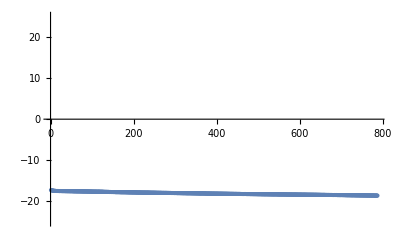
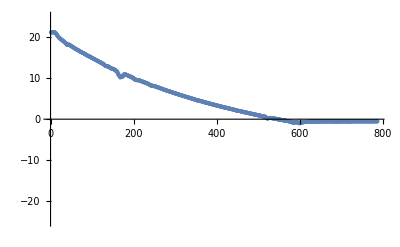
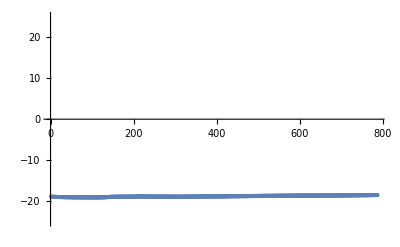
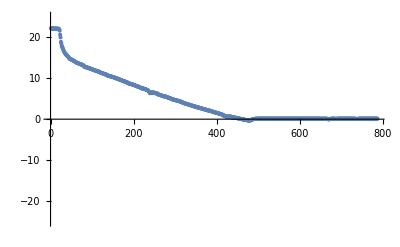

```mathematica
Map[plotBasicTemperatureProfiles[#,Length[rawDataMeasurement1T[[1]]]]&,Drop[rawDataMeasurement1T,1]]
```

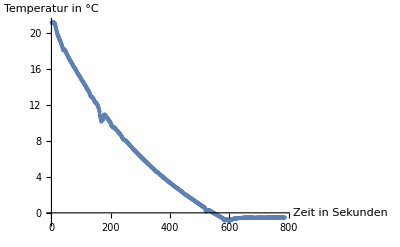

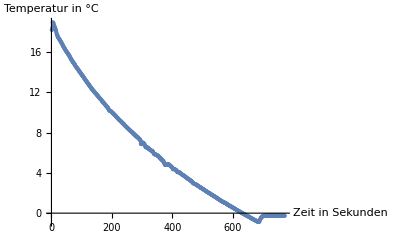

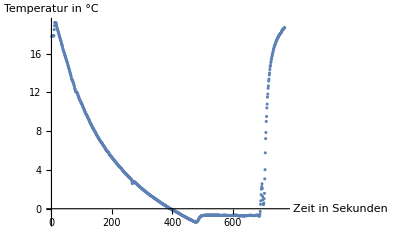

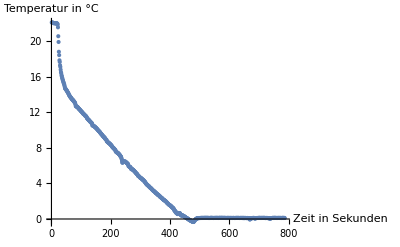

```mathematica
saccharosePlot=ListPlot[rawDataMeasurement1T[[3]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"}]
veWasser1Plot=ListPlot[rawDataMeasurement2T[[3]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"}]
glucosePlot=ListPlot[rawDataMeasurement2T[[5]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"}]
veWasser2Plot=ListPlot[rawDataMeasurement1T[[5]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"}]
```

```mathematica
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotSaccharose.pdf",saccharosePlot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotGlucose.pdf",glucosePlot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotVeWasser1.pdf",veWasser1Plot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotVeWasser2.pdf",veWasser2Plot]
```

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotSaccharose.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotGlucose.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotVeWasser1.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotVeWasser2.pdf

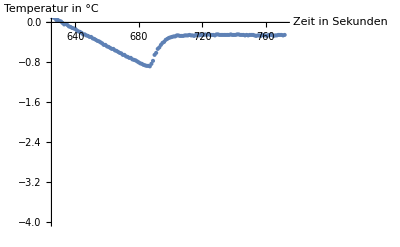

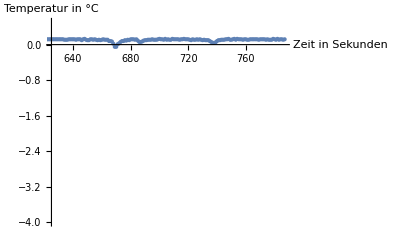

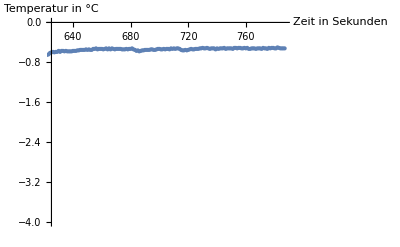

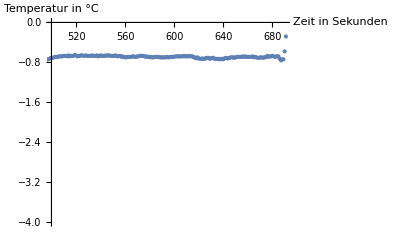

```mathematica
veWasser1ZoomedPlot=ListPlot[rawDataMeasurement2T[[3]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"},PlotRange->{{625,Length[rawDataMeasurement2T[[3]]]},{-4,0}}]
veWasser2ZoomedPlot=ListPlot[rawDataMeasurement1T[[5]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"},PlotRange->{{625,Length[rawDataMeasurement1T[[5]]]},{-4,0.5}}]
saccharoseZoomedPlot=ListPlot[rawDataMeasurement1T[[3]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"},PlotRange->{{625,Length[rawDataMeasurement1T[[3]]]},{-4,0}}]
glucoseZoomedPlot=ListPlot[rawDataMeasurement2T[[5]],AxesLabel->{"Zeit in Sekunden","Temperatur in °C"},PlotRange->{{500,690},{-4,0}}]
```

```mathematica
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotZoomedSaccharose.pdf",saccharoseZoomedPlot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotZoomedGlucose.pdf",glucoseZoomedPlot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotZoomedVeWasser1.pdf",veWasser1ZoomedPlot]
Export["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v1\\results\\graphics\\plotZoomedVeWasser2.pdf",veWasser2ZoomedPlot]
```

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotZoomedSaccharose.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotZoomedGlucose.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotZoomedVeWasser1.pdf

C:\Users\martin\github_repos\THERMO-EDA\v1\results\graphics\plotZoomedVeWasser2.pdf